## Settings

```mathematica
imgsize=700;
SetDirectory@NotebookDirectory[];
```

```mathematica
eqn = D[D[f[x],x],x]-( a k Cot[k x]+i(omegam - a Sin[k x]Cos[2thetam]) a Sin[k x] )D[f[x],x]+(Sin[2 thetam]/2)^2 a^2 Sin[k x]^2 f[x]==0
```

1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0

```mathematica
DSolve[eqn,f[x],x]
```

DSolve[1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0,f[x],x]

```mathematica
DSolve[f[x]+x D[f[x],x]==omegam/2-deltalambda[x]Sin[2thetam]/2,f[x],x]
```

{{f[x]→C[1]/x+(∫_1^x 1/2 (omegam-deltalambda[K[1]] Sin[2 thetam])ⅆK[1])/x}}

```mathematica
sys=I D[{phi1[x],phi2[x]},x]=={{0,(g0R+I g0I) Exp[I(-omegam+n0 k)x]},{(g0R-I g0I) Exp[-I(-omegam+n0 k)x],0}}.{phi1[x],phi2[x]}
```

{ⅈ phi1'[x],ⅈ phi2'[x]}=={ⅇ^(ⅈ (k n0-omegam) x) (ⅈ g0I+g0R) phi2[x],ⅇ^(-ⅈ (k n0-omegam) x) (-ⅈ g0I+g0R) phi1[x]}

```mathematica
DSolve[sys,{phi1,phi2},x]
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

```mathematica
%//FullSimplify
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

## Understand The Hamiltonian

```mathematica
ClearAll[k,x,phi,function1,constant1]
DSolve[I D[function1[x],x]==constant1 Sin[k x+phi]function1[x],function1,x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-ⅈ constant1 (-(Cos[phi] Cos[k x])/k+(Sin[phi] Sin[k x])/k)) C[1]]}}

```mathematica
ClearAll[a,k,x,phi,function1,constant1]
DSolve[D[D[function1[x],x],x]-D[a Sin[k x + phi],x]/(a Sin[k x + phi])D[function1[x],x]==-Sin[2thetam]^2/4(a Sin[k x + phi])^2 function1[x],function1,x]
```

{{function1→Function[{x},C[1] Cos[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]-C[2] Sin[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]]}}

## Constant Matter ‘Perturbation’

```mathematica
ClearAll[k,x,phi,function1,function2,constant1]
DSolve[I D[{function1[x],function2[x]},x]==Sin[2thetam]/2 lambdac{{0,Exp[I Cos[2thetam]lambdac x-I omegam x]},{Exp[-I Cos[2thetam]lambdac x + I omegam x],0}}.{function1[x],function2[x]},{function1,function2},x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1]+ⅇ^(1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2]],function2→Function[{x},1/lambdac ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1] (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]+1/lambdac ⅈ ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]+1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2] (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]]}}

## Investigate Resonance

Define the amplitude

```mathematica
ClearAll[khat,ahat,thetam,thetamV,zk,n0,x,phi,function1,function2,constant1]
```

```mathematica
thetamV=Pi/5;
aV=1;
phiV=0;
```

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/2 ahat Sin[2thetam](2n0)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = ( Abs[fun[khat,ahat,thetam,n0]]^2)/( Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/((-1+khat n0)^2+Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2)

```mathematica
(*Limit[amplitude[k,a,t,Round[k]],k->Infinity]*)
```

```mathematica
Limit[amplitude[k,a,t,Round[k]],t->0]
(*Limit[amplitude[k,a,t],t->Pi/4]*)
```

0

```mathematica
Table[{amplitude[k,0.1,Pi/5,Round[k]],k},{k,0.1,1,0.1}]
```

{{0.,0.1},{0.,0.2},{0.,0.3},{0.,0.4},{0.,0.5},{0.0139269,0.6},{0.0244978,0.7},{0.0534881,0.8},{0.18438,0.9},{1.,1.}}

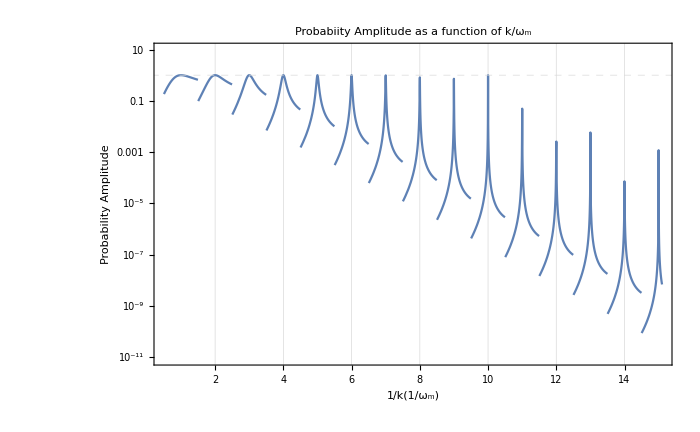

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(1/ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m"]
```

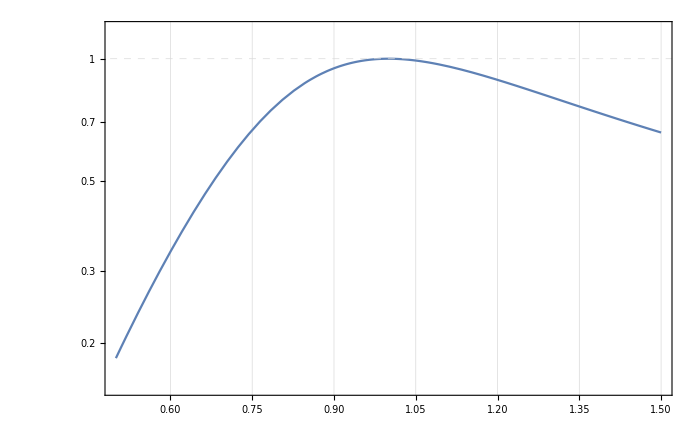

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,1.5},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]]
```

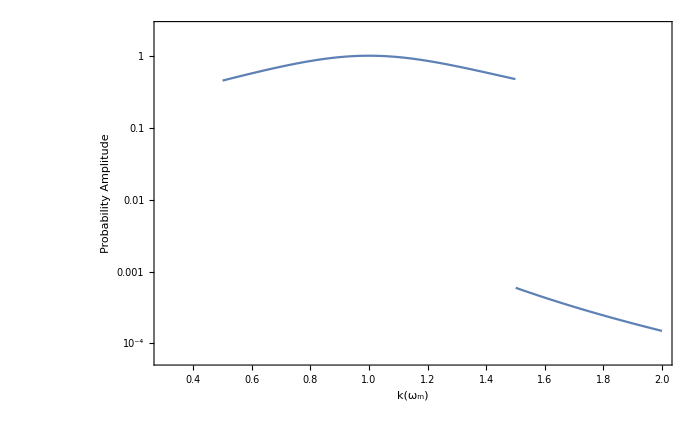

```mathematica
LogPlot[amplitude[k,aV,thetamV,Round[k]],{k,0.3,2},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full]
```

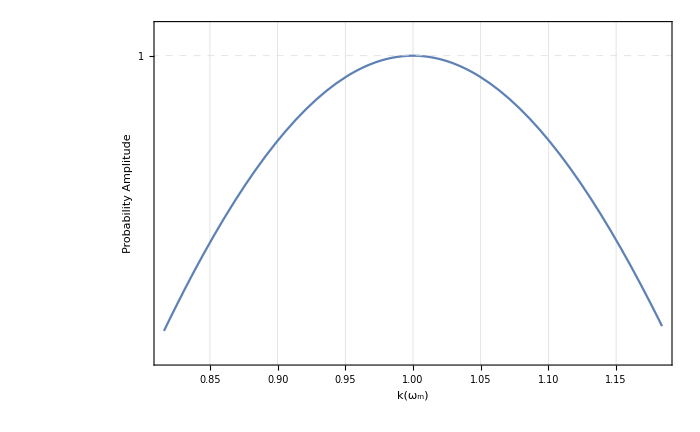
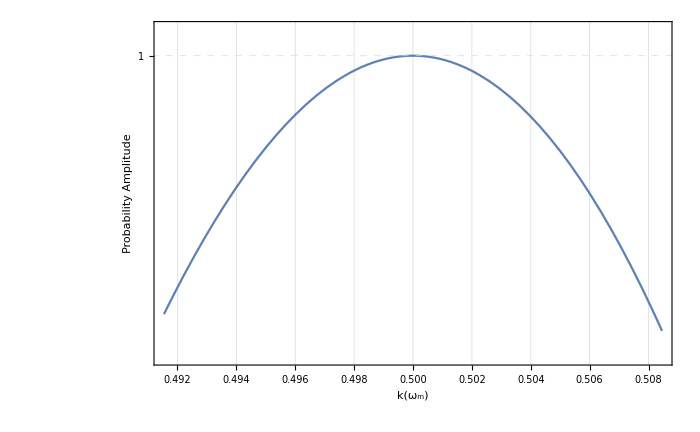
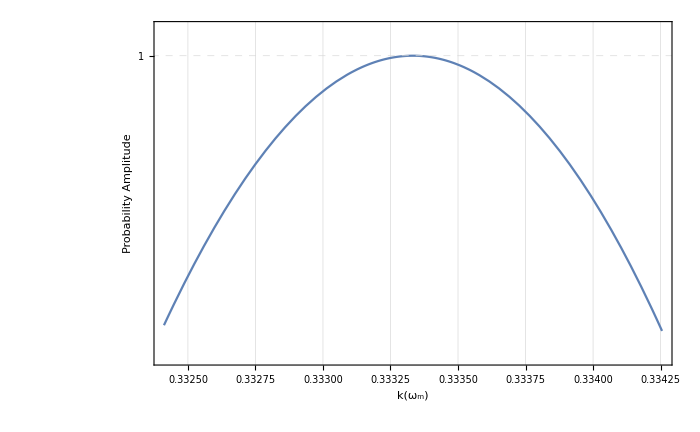
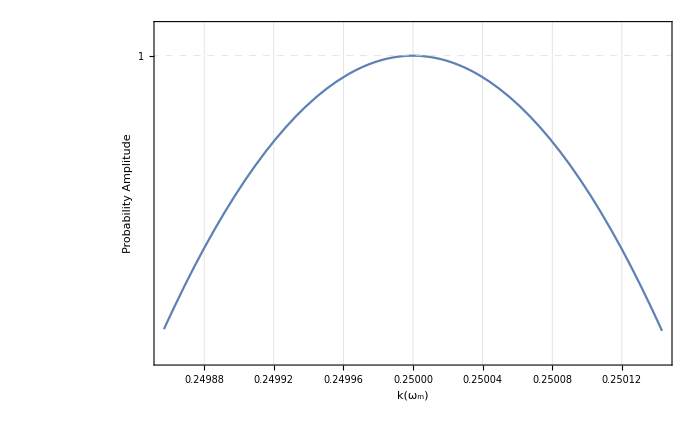

```mathematica
Table[LogPlot[amplitude[k,aV,thetamV,n],{k,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]],{n,1,4}]
```

```mathematica
Series[BesselJ[0,x],{x,0,3}]
```

1-x^2/4+O[x]^4

```mathematica
Limit[BesselJ[0,x]/x,x->0]
```

∞

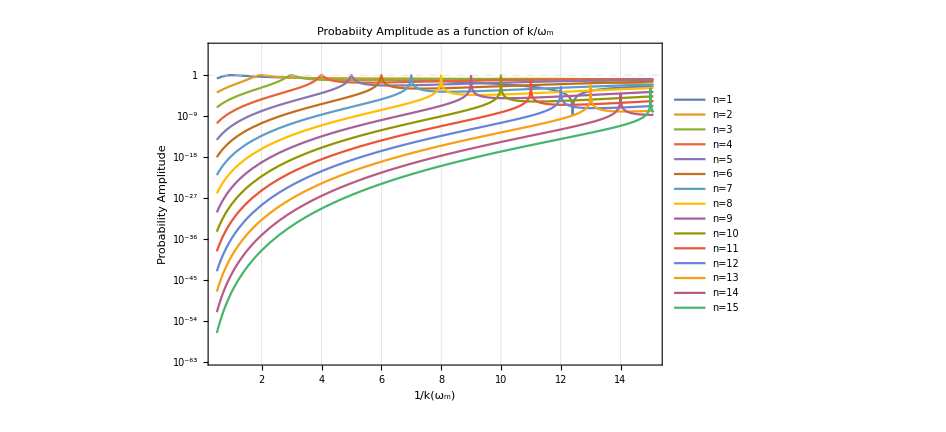

```mathematica
listFunctions=Table[amplitude[1/k,aV,thetamV,n],{n,1,15,1}];
listFunctionsLegends=Table["n="<>ToString@n,{n,1,15,1}];
LogPlot[listFunctions,{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m",PlotLegends->listFunctionsLegends]
```

### Investigation on Width

Looking for the width

```mathematica
aWV=0.1
endpointWList=10
```

0.1

10

```mathematica
fwhm[n_]:=Abs@First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-1/n)/n&&k<(1+1/n)/n, k]}]
fwhmRange[n_]:=First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-0.5/Exp[n]/n^2)/n&&k<(1+0.5/Exp[n]/n^2)/n, k]}]
fwhmFR[n_]:=2*(k - n) /. FindRoot[amplitude[k,aWV,thetamV, n] == 0.5, {k,1/n,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n}];
```

```mathematica
fwhm[1]
fwhmRange[1]
fwhm[7]
```

0.0950942

0.0950942

$Aborted

```mathematica
widthList=Table[{i,fwhmRange[i]},{i,1,endpointWList}](*For pertubation amplitude equals 0.1*)
(*widthList=Table[{i,fwhm[i]},{i,1,endpointWList}]*)(*For large perturbation amplitude*)
widthListLog=Table[{widthList[[i,1]],Log@widthList[[i,2]]},{i,1,endpointWList}];
widthLine=Fit[widthListLog,{1,x},x];(*Fit data of {x,Log[y]}*)
```

{{1,0.0950942},{2,0.001469},{3,0.0000340384},{4,9.34761×10^-7},{5,2.82022×10^-8},{6,9.03355×10^-10},{7,3.01608×10^-11},{8,1.03811×10^-12},{9,3.6568×10^-14},{10,k/.{ToRules[Reduce[(100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)/((-1+10 k)^2+100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)==0.5&&k>0.1&&k<0.1,k]]}}}

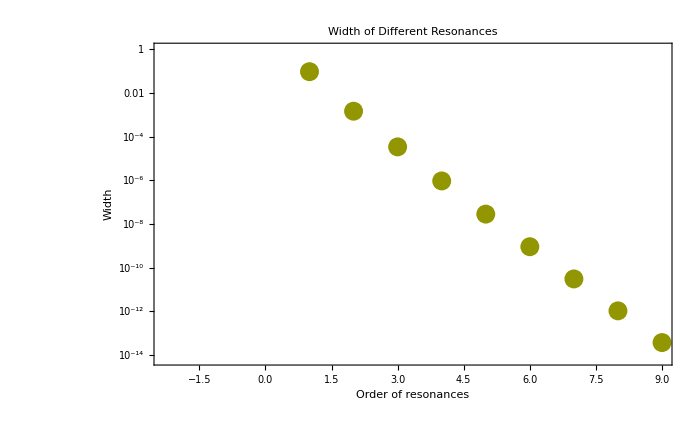

```mathematica
widthListPlt=ListLogPlot[widthList,ImageSize->imgsize,Frame->True,FrameLabel->{"Order of resonances","Width"},PlotLabel->"Width of Different Resonances"]
```

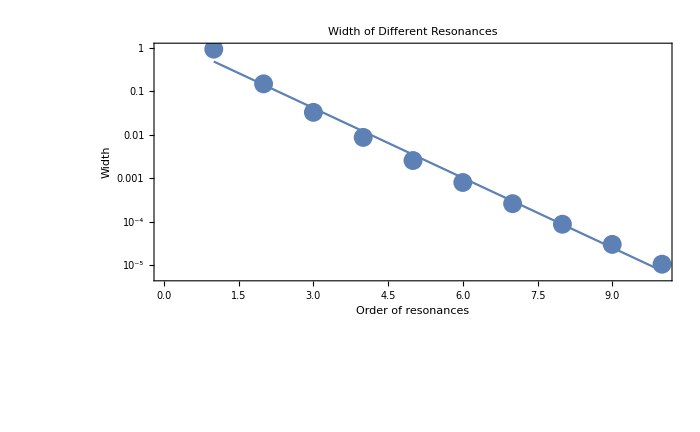

```mathematica
widthLinePlt=Plot[widthLine,{x,1,10},ImageSize->imgsize,Frame->True];
Show[widthListPlt,widthLinePlt,Epilog->Inset[Framed[Style["Line: "<>ToString[widthLine],20],Background->White],{3,-30}]]
```

#### Some Approximation?

The amplitude has a F^2/(F^2+g^2) form, we assume the bessel function dosn’t change a lot during the resonance. Thus we have the width

```mathematica
widthLor[thetam_,ahat_,n0_]:=N@ 2Tan[2thetam] 1/n0 BesselJ[n0,ahat n0 Cos[2thetam]]
```

```mathematica
widthLor[thetamV,aWV,1]
```

0.0950943

```mathematica
widthLorList=Table[{i,widthLor[thetamV,aWV,i]},{i,1,10}]
```

{{1,0.0950943},{2,0.001469},{3,0.0000340384},{4,9.34761×10^-7},{5,2.82022×10^-8},{6,9.03355×10^-10},{7,3.01608×10^-11},{8,1.03811×10^-12},{9,3.65732×10^-14},{10,1.31242×10^-15}}

```mathematica
widthDiffList=Table[{i,(widthList[[i,2]]-widthLorList[[i,2]])/widthList[[i,2]]},{i,1,10}]
```

{{1,-8.12469×10^-7},{2,4.30976×10^-6},{3,1.82264×10^-8},{4,2.30759×10^-11},{5,7.25243×10^-10},{6,5.44596×10^-9},{7,-8.44821×10^-8},{8,2.46072×10^-7},{9,-0.00014181},{10,(-1.31242×10^-15+(k/.{ToRules[Reduce[(100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)/((-1+10 k)^2+100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)==0.5&&k>0.1&&k<0.1,k]]}))/(k/.{ToRules[Reduce[(100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)/((-1+10 k)^2+100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)==0.5&&k>0.1&&k<0.1,k]]})}}

```mathematica
ListLogPlot[{widthLorList,widthList},PlotLegends->Placed[{"Approximation","Numerical"},{Top,Center}],Frame->True,ImageSize->imgsize,PlotRange->{{0,endpointWList-1},Automatic},PlotMarkers->{{"+",Large},{"x",Large}},PlotLabel->"Comparison of Approximated Width and Numerical Width"]
(*Export["export/stimulated-single-frequency-width-approximation.png",%]*)
```

-Graphics-

export/stimulated-single-frequency-width-approximation-amp-point1.png

#### What is Bessel Function

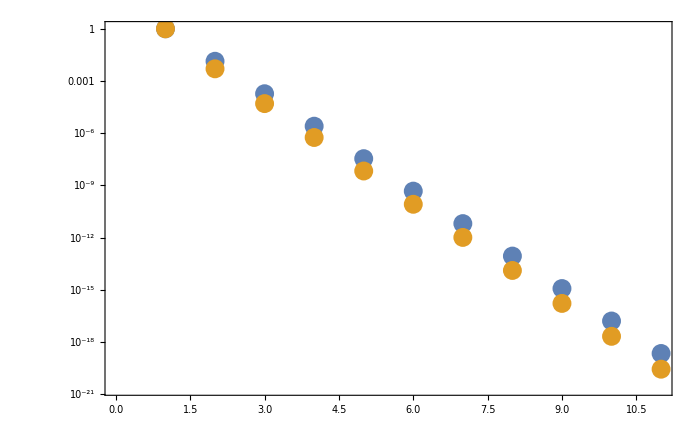

```mathematica
delta=0.01;
besselJApprox[n_]:=Exp[n](delta/2)^n;
ListLogPlot[{Table[besselJApprox[n],{n,0,10}],Table[BesselJ[n,n*delta],{n,0,10}]},Frame->True,ImageSize->imgsize]
```

## Comparing Numerical with Approximation

```mathematica
thetamN=Pi/5;
phiN=0;
kN=0.95;
aN=0.1(kN)^(-5/3);
endpointN=400;
init={psi1[0],psi2[0]}=={1,0};
```

```mathematica
amplitude[kN,aN,thetamN,1]
```

0.517568

```mathematica
probApprox[x_,nN_]:=amplitude[kN,aN,thetamN,nN](Sin[Sqrt[ Abs[fun[kN,aN,thetamN,nN]]^2+(nN kN - 1)^2]x/2])^2;
```

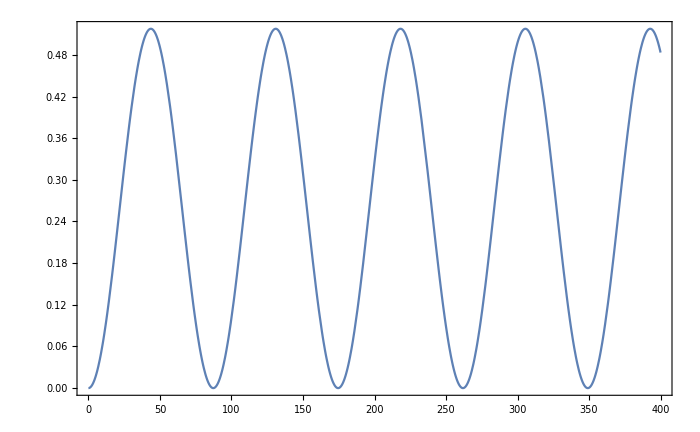

```mathematica
pltProbApprox=Plot[probApprox[x,1],{x,0,endpointN},Frame->True,ImageSize->imgsize]
```

```mathematica
hN[x_]:=(aN Sin[kN x+phiN])Sin[2thetamN]Exp[I(-x-Cos[2thetamN] aN/kN Cos[kN x+phiN])]/2;
```

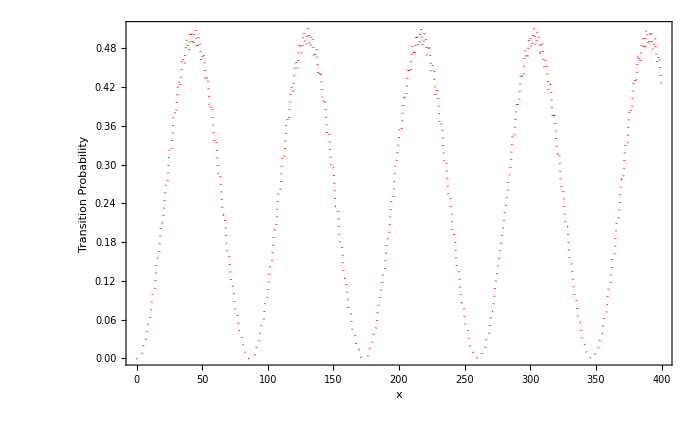

```mathematica
solN=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hN[x]},{Conjugate[hN[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointN}];

pltN=Plot[Evaluate[Abs[psi2[x]]^2/.solN],{x,0,endpointN},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->{Dotted,Red}]
```

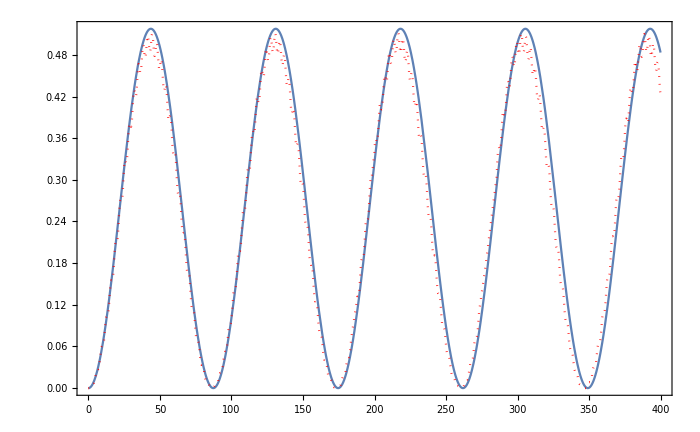

```mathematica
Show[pltProbApprox,pltN]
```

## Transition VS Noise Amplitude (Alex)

```mathematica
thetamPA=Pi/5;
pertAmpMani=Manipulate[ListPlot[Table[{perturbAmp,amplitude[kPA,perturbAmp,thetamPA,Round[kPA]]},{perturbAmp,0.01,2,0.01}],Frame->True,ImageSize->imgsize,FrameLabel->{"Perturbation Amplitude","Transition Probability Amplitude"},PlotRange->{Automatic,{0,1}}],{{kPA,0.5,"Matter Perturbation Frequency"},0.5,1.5,LabeledSlider}]
```

```mathematica
Export["export/k-perturbation-amplitude-trans-amp.avi",pertAmpMani]
```

export/k-perturbation-amplitude-trans-amp.avi

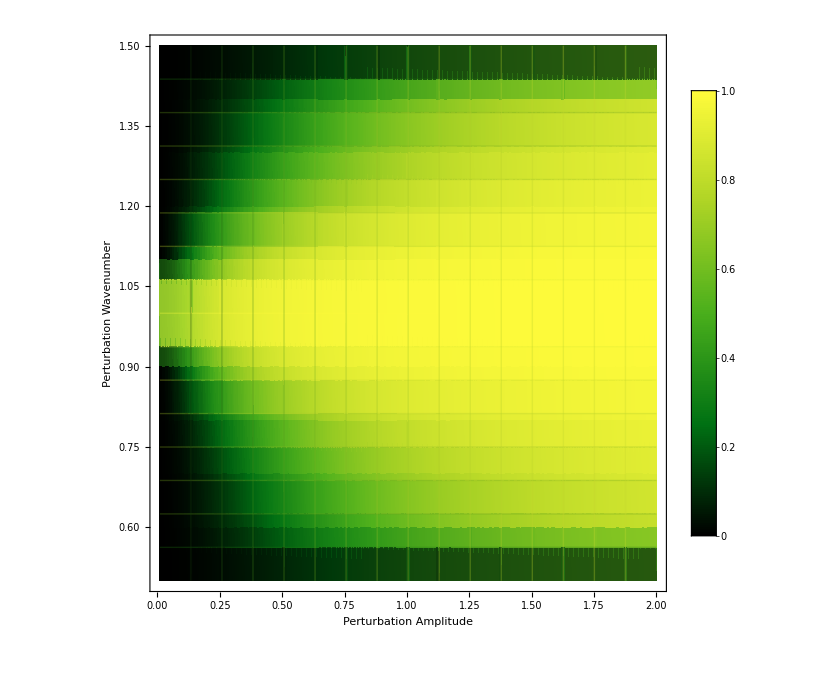

```mathematica
thetamPAk=Pi/5;
ampPAkList=Flatten[Table[{perturbAmp,kPAk,amplitude[kPAk,perturbAmp,thetamPA,Round[kPAk]]},{perturbAmp,0.01,2,0.01},{kPAk,0.5,1.5,0.1}],1];
ListPlot3D[ampPAkList,ImageSize->imgsize,AxesLabel->{"Perturbation Amplitude","Perturbation Frequency","Probability Amplitude"}];
pltPertAmpPertWaveNumTransitionAmp=ListDensityPlot[ampPAkList,Mesh->Automatic,FrameLabel->{"Perturbation Amplitude","Perturbation Wavenumber"},ColorFunction->"AvocadoColors",PlotLegends->Automatic,ImageSize->imgsize]
```

```mathematica
Export["export/pltPertAmpPertWaveNumTransitionAmp.svg",pltPertAmpPertWaveNumTransitionAmp]
```

export/pltPertAmpPertWaveNumTransitionAmp.svg

### Resonance width due to different perturbation amplitude

```mathematica
fwhmAmp[n_,pertAmp_]:=Abs@First@Differences[k/.{ToRules@Reduce[amplitude[k,pertAmp,thetamV, n] == 0.5&&k>(1-1/n)/n&&k<(1+1/n)/n, k]}]
```

```mathematica
fwhmAmpList=Table[{amp,fwhmAmp[10,amp]},{amp,0.1,1.5,0.1}]
```

{{0.1,1.31839×10^-15},{0.2,1.3352×10^-12},{0.3,7.61618×10^-11},{0.4,1.33202×10^-9},{0.5,1.21646×10^-8},{0.6,7.35334×10^-8},{0.7,3.3389×10^-7},{0.8,1.22811×10^-6},{0.9,3.84171×10^-6},{1.,0.0000105655},{1.1,0.0000261585},{1.2,0.0000593308},{1.3,0.000124924},{1.4,0.000246718},{1.5,0.000460827}}

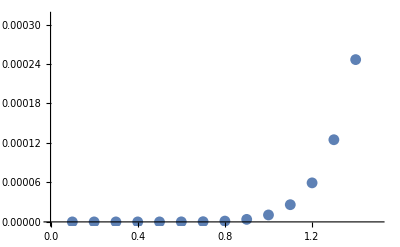

```mathematica
ListPlot[fwhmAmpList]
```

```mathematica
fwhmNAmpList=Table[{n,amp,fwhmAmp[n,amp]},{amp,0.1,1.5,0.1},{n,1,10}]
```

{{{1,0.1,0.0950942},{2,0.1,0.001469},{3,0.1,0.0000340384},{4,0.1,9.34761×10^-7},{5,0.1,2.82022×10^-8},{6,0.1,Abs[First[{}]]},{7,0.1,3.01608×10^-11},{8,0.1,1.03811×10^-12},{9,0.1,3.6568×10^-14},{10,0.1,1.31839×10^-15}},{{1,0.2,0.190118},{2,0.2,0.00587077},{3,0.2,0.000271869},{4,0.2,0.0000149219},{5,0.2,8.99779×10^-7},{6,0.2,5.76021×10^-8},{7,0.2,3.84368×10^-9},{8,0.2,2.64407×10^-10},{9,0.2,1.86171×10^-11},{10,0.2,1.3352×10^-12}},{{1,0.3,0.284991},{2,0.3,0.0131919},{3,0.3,0.000915106},{4,0.3,0.000075254},{5,0.3,6.79877×10^-6},{6,0.3,6.52105×10^-7},{7,0.3,6.5194×10^-8},{8,0.3,6.71911×10^-9},{9,0.3,7.08809×10^-10},{10,0.3,7.61618×10^-11}},{{1,0.4,0.379613},{2,0.4,0.023417},{3,0.4,0.00216112},{4,0.4,0.00023657},{5,0.4,0.0000284508},{6,0.4,3.63254×10^-6},{7,0.4,4.8342×10^-7},{8,0.4,6.63208×10^-8},{9,0.4,9.31293×10^-9},{10,0.4,1.33202×10^-9}},{{1,0.5,0.47385},{2,0.5,0.0365393},{3,0.5,0.00420136},{4,0.5,0.000573605},{5,0.5,0.000086049},{6,0.5,0.0000137043},{7,0.5,2.27489×10^-6},{8,0.5,3.89288×10^-7},{9,0.5,6.81853×10^-8},{10,0.5,1.21646×10^-8}},{{1,0.6,0.567514},{2,0.6,0.0525734},{3,0.6,0.00722078},{4,0.6,0.00117951},{5,0.6,0.000211779},{6,0.6,0.0000403693},{7,0.6,8.02063×10^-6},{8,0.6,1.64274×10^-6},{9,0.6,3.44377×10^-7},{10,0.6,7.35334×10^-8}},{{1,0.7,0.660343},{2,0.7,0.0715721},{3,0.7,0.0113992},{4,0.7,0.00216387},{5,0.7,0.000451831},{6,0.7,0.000100174},{7,0.7,0.0000231485},{8,0.7,5.51428×10^-6},{9,0.7,1.34448×10^-6},{10,0.7,3.3389×10^-7}},{{1,0.8,0.751972},{2,0.8,0.0936473},{3,0.8,0.0169164},{4,0.8,0.00365086},{5,0.8,0.00086784},{6,0.8,0.000219101},{7,0.8,0.0000576571},{8,0.8,0.0000156407},{9,0.8,4.34269×10^-6},{10,0.8,1.22811×10^-6}},{{1,0.9,0.841902},{2,0.9,0.118999},{3,0.9,0.0239622},{4,0.9,0.00577808},{5,0.9,0.00153775},{6,0.9,0.000434923},{7,0.9,0.000128233},{8,0.9,0.000038975},{9,0.9,0.0000121246},{10,0.9,3.84171×10^-6}},{{1,1.,0.929482},{2,1.,0.147957},{3,1.,0.0327556},{4,1.,0.00869769},{5,1.,0.00255633},{6,1.,0.000799364},{7,1.,0.000260656},{8,1.,0.0000876234},{9,1.,0.0000301487},{10,1.,0.0000105655}},{{1,1.1,1.01393},{2,1.1,0.181049},{3,1.1,0.0435784},{4,1.1,0.0125819},{5,1.1,0.00403604},{6,1.1,0.00138},{7,1.1,0.000492356},{8,1.1,0.00018113},{9,1.1,0.0000682048},{10,1.1,0.0000261585}},{{1,1.2,1.09441},{2,1.2,0.219095},{3,1.2,0.056838},{4,1.2,0.017637},{5,1.2,0.00610955},{6,1.2,0.0022621},{7,1.2,0.000874985},{8,1.2,0.000349127},{9,1.2,0.000142606},{10,1.2,0.0000593308}},{{1,1.3,1.17024},{2,1.3,0.263274},{3,1.3,0.0732},{4,1.3,0.024135},{5,1.3,0.00893698},{6,1.3,0.00355118},{7,1.3,0.00147703},{8,1.3,0.000634246},{9,1.3,0.000278892},{10,1.3,0.000124924}},{{1,1.4,1.24102},{2,1.4,0.314509},{3,1.4,0.0939224},{4,1.4,0.0324835},{5,1.4,0.012724},{6,1.4,0.00537847},{7,1.4,0.00238693},{8,1.4,0.00109525},{9,1.4,0.000514969},{10,1.4,0.000246718}},{{1,1.5,1.30679},{2,1.5,0.368822},{3,1.5,0.12199},{4,1.5,0.0434042},{5,1.5,0.0177654},{6,1.5,0.00791412},{7,1.5,0.00371846},{8,1.5,0.0018108},{9,1.5,0.000904693},{10,1.5,0.000460827}}}

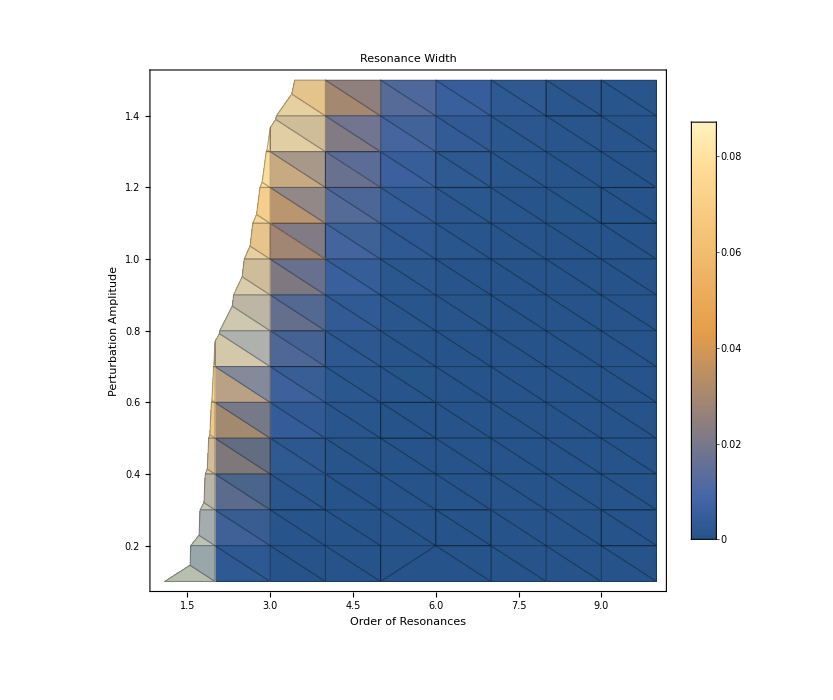

```mathematica
ListDensityPlot[Select[Table[Flatten[fwhmNAmpList,1][[i]],{i,1,Length@Flatten[fwhmNAmpList,1]}],#[[3]]>0&],FrameLabel->{"Order of Resonances","Perturbation Amplitude"},ImageSize->imgsize,PlotLabel->"Resonance Width",PlotLegends->Automatic,Mesh->All]
```

## Analytical Analysis

The Width?

```mathematica
Series[BesselJ[n,x],{x,n a Cos[2thetam],3}]//FullSimplify
```

BesselJ[n,a n Cos[2 thetam]]+(-BesselJ[1+n,a n Cos[2 thetam]]+(BesselJ[n,a n Cos[2 thetam]] Sec[2 thetam])/a) (x-a n Cos[2 thetam])+1/(2 a^2 n)(a BesselJ[1+n,a n Cos[2 thetam]] Sec[2 thetam]-BesselJ[n,a n Cos[2 thetam]] (a^2 n-(-1+n) Sec[2 thetam]^2)) (x-a n Cos[2 thetam])^2+1/(6 a^3 n^2)(-1/2 (-1+n) BesselJ[n,a n Cos[2 thetam]] (4+(-2+a^2) n+a^2 n Cos[4 thetam]) Sec[2 thetam]^3+a BesselJ[1+n,a n Cos[2 thetam]] (a^2 n^2-(2+n^2) Sec[2 thetam]^2)) (x-a n Cos[2 thetam])^3+O[x-a n Cos[2 thetam]]^4

```mathematica
Series[1/(k0+k1),{k1,0,3}]
```

1/k0-k1/k0^2+k1^2/k0^3-k1^3/k0^4+O[k1]^4

```mathematica
Series[((1-n0 k1 +n0^2k1^2))^(2m+n),{k1,0,2}]//FullSimplify
```

1-(2 m+n) n0 k1+1/2 (2 m+n) (1+2 m+n) n0^2 k1^2+O[k1]^3

```mathematica
fterm=1/2 Tan[2thetam](2n+1)(1/n+k1)(bes0-bes1 k1+bes2 k1^2);
Collect[fterm^2,k1]
```

1/4 bes2^2 k1^6 (1+2 n)^2 Tan[2 thetam]^2+1/4 k1 (-(2 bes0 bes1)/n^2+(2 bes0^2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^2 (bes0^2+bes1^2/n^2+(2 bes0 bes2)/n^2-(4 bes0 bes1)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^3 (-2 bes0 bes1-(2 bes1 bes2)/n^2+(2 bes1^2)/n+(4 bes0 bes2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^4 (bes1^2+2 bes0 bes2+bes2^2/n^2-(4 bes1 bes2)/n) (1+2 n)^2 Tan[2 thetam]^2+1/4 k1^5 (-2 bes1 bes2+(2 bes2^2)/n) (1+2 n)^2 Tan[2 thetam]^2+(bes0^2 (1+2 n)^2 Tan[2 thetam]^2)/(4 n^2)

```mathematica
gterm=n(1/n+k1)-1;
Collect[gterm^2,k1]
```

k1^2 n^2

```mathematica
Solve[c0+c1 x+(c2-n^2) x^2==0,x]
```

{{x→(-c1-√(c1^2-4 c0 c2+4 c0 n^2))/(2 (c2-n^2))},{x→(-c1+√(c1^2-4 c0 c2+4 c0 n^2))/(2 (c2-n^2))}}

```mathematica
testNDep[c0_,c1_,c2_,n_]:=(√(c1^2-4c0(c2-n^2)))/(c2-n^2)
```

```mathematica
Manipulate[Plot[testNDep[c0,c1,c2,n],{n,1,10}],{c0,0,1},{c1,0,1},{c2,0,1}]
```

Calculate the width of a distribution

```mathematica
ClearAll[gamma,f,x,k]
Solve[f^2/(f^2+(n k-1)^2)/Pi==0.5,k]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{k→-(0.159155 (-6.28319 n-(0.+3.78757 ⅈ) f n))/n^2},{k→-(0.159155 (-6.28319 n+(0.+3.78757 ⅈ) f n))/n^2}}